AWGN PSK BLER :

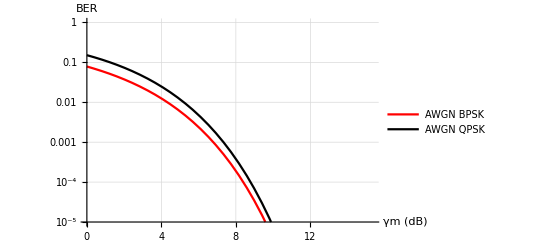

```mathematica
Q[z_]:=1/2 Erfc[z/(√2)];probError[γm_]:=Q[√(2 10^(γm/10))];PNm[γm_,N_,m_]:=((N!)/(m!(N-m)!))×(1-probError[γm])^(N-m)×(probError[γm])^m;PeM[γm_,N_]:= 1 - PNm[γm,N,0];
LogPlot[{PeM[γm,1], PeM[γm,2]},{γm,0,20},AxesLabel->{"γm (dB)","BER"},PlotRange->{10^-5,1}, PlotStyle->{Red, Black},PlotLegends->{"AWGN BPSK","AWGN QPSK"},GridLines->Automatic]
```

AWGN QAM BLER:

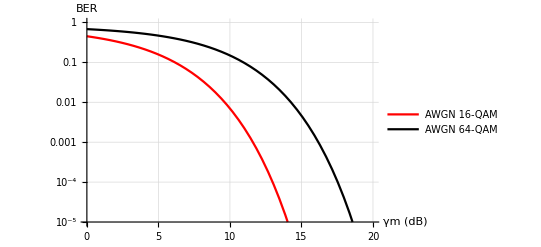

```mathematica
Q[z_]:=1/2 Erfc[z/(√2)];
probErrorQAM[γm_, L_]:=4/Log[2,L](1-1/(√L))Q[√((3 Log[2,L])/(L-1)10^(γm/10))];PNmQAM[γm_,L_,N_,m_]:=((N!)/(m!(N-m)!))×(1-probErrorQAM[γm, L])^(N-m)×(probErrorQAM[γm, L])^m;PeMQAM[γm_,L_,N_]:= 1 - PNmQAM[γm,L,N,0];LogPlot[{PeMQAM[γm,16,4], PeMQAM[γm,64,6]},{γm,0,20},AxesLabel->{"γm (dB)","BER"},PlotRange->{10^-5,1}, PlotStyle->{Red, Black},PlotLegends->{"AWGN 16-QAM","AWGN 64-QAM"},GridLines->Automatic]
```

BLER AWGN OVER DIFFERENT MODULATIONS:

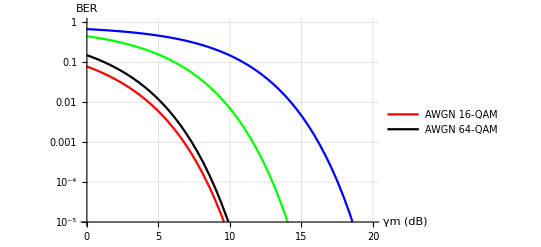

```mathematica
LogPlot[{PeM[γm,1], PeM[γm,2],PeMQAM[γm,16,4], PeMQAM[γm,64,6]},{γm,0,20},AxesLabel->{"γm (dB)","BER"},PlotRange->{10^-5,1}, PlotStyle->{Red, Black, Green, Blue},PlotLegends->{"AWGN 16-QAM","AWGN 64-QAM"},GridLines->Automatic]
```